```mathematica
D[s[η],{η,2}]==2/3s[η]^3
DSolve[%, s[η],η]
```

s''[η]==(2 s[η]^3)/3

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{s[η]→-3^(1/4) √(ⅈ/(√C[1])) √C[1] JacobiSN[((-1)^(3/4) √(√3 η^2 √C[1]+2 √3 η √C[1] C[2]+√3 √C[1] C[2]^2))/(√3),-1]},{s[η]→3^(1/4) √(ⅈ/(√C[1])) √C[1] JacobiSN[((-1)^(3/4) √(√3 η^2 √C[1]+2 √3 η √C[1] C[2]+√3 √C[1] C[2]^2))/(√3),-1]}}

-(JacobiDN[η/(√3),1/2] JacobiSN[η/(√3),1/2])/JacobiCN[η/(√3),1/2]

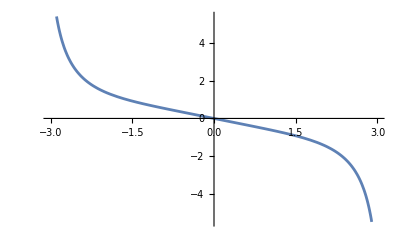

```mathematica
-JacobiSN[η/Sqrt[3],1/2]/JacobiCN[η/Sqrt[3],1/2]*JacobiDN[η/Sqrt[3],1/2]
Plot[%,{η,-3,3}]
```

```mathematica
f1[η_]:=-JacobiSN[η/Sqrt[3],1/2]/JacobiCN[η/Sqrt[3],1/2]*JacobiDN[η/Sqrt[3],1/2]
f1''[η]-2/3f1[η]^3//FullSimplify
```

0

```mathematica
D[s[η],{η,2}]+2/3s[η]==2/3s[η]^3
DSolve[%, s[η],η]
```

(2 s[η])/3+s''[η]==(2 s[η]^3)/3

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{s[η]→ⅈ √(-1/(1-√(1-3 C[1]))) JacobiSN[(√(η^2+η^2 √(1-3 C[1])+2 η C[2]+2 η √(1-3 C[1]) C[2]+C[2]^2+√(1-3 C[1]) C[2]^2))/(√3),(1-√(1-3 C[1]))/(1+√(1-3 C[1]))]-ⅈ √(-1/(1-√(1-3 C[1]))) √(1-3 C[1]) JacobiSN[(√(η^2+η^2 √(1-3 C[1])+2 η C[2]+2 η √(1-3 C[1]) C[2]+C[2]^2+√(1-3 C[1]) C[2]^2))/(√3),(1-√(1-3 C[1]))/(1+√(1-3 C[1]))]},{s[η]→-ⅈ √(-1/(1-√(1-3 C[1]))) JacobiSN[(√(η^2+η^2 √(1-3 C[1])+2 η C[2]+2 η √(1-3 C[1]) C[2]+C[2]^2+√(1-3 C[1]) C[2]^2))/(√3),(1-√(1-3 C[1]))/(1+√(1-3 C[1]))]+ⅈ √(-1/(1-√(1-3 C[1]))) √(1-3 C[1]) JacobiSN[(√(η^2+η^2 √(1-3 C[1])+2 η C[2]+2 η √(1-3 C[1]) C[2]+C[2]^2+√(1-3 C[1]) C[2]^2))/(√3),(1-√(1-3 C[1]))/(1+√(1-3 C[1]))]}}

```mathematica
f2[η_]:=-JacobiSN[η/Sqrt[3],A]/JacobiCN[η/Sqrt[3],A]*JacobiDN[η/Sqrt[3],A]
f2''[η]+2/3f2[η]-2/3f2[η]^3//FullSimplify
FindInstance[%==0,A]
```

(4 (-1+A) JacobiDN[η/(√3),A] JacobiSN[η/(√3),A])/(3 JacobiCN[η/(√3),A])

FindInstance::exvar: The system contains a nonconstant expression η independent of variables {A}.

FindInstance[(4 (-1+A) JacobiDN[η/(√3),A] JacobiSN[η/(√3),A])/(3 JacobiCN[η/(√3),A])==0,A]

```mathematica
D[s[η],{η,2}]-2/3s[η]==2/3s[η]^3
DSolve[%, s[η],η]
```

-(2 s[η])/3+s''[η]==(2 s[η]^3)/3

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{s[η]→-ⅈ √(1+√(1-3 C[1])) JacobiSN[(√(-η^2+η^2 √(1-3 C[1])-2 η C[2]+2 η √(1-3 C[1]) C[2]-C[2]^2+√(1-3 C[1]) C[2]^2))/(√3),(1+√(1-3 C[1]))/(1-√(1-3 C[1]))]},{s[η]→ⅈ √(1+√(1-3 C[1])) JacobiSN[(√(-η^2+η^2 √(1-3 C[1])-2 η C[2]+2 η √(1-3 C[1]) C[2]-C[2]^2+√(1-3 C[1]) C[2]^2))/(√3),(1+√(1-3 C[1]))/(1-√(1-3 C[1]))]}}

```mathematica
-JacobiSN[A*η,B]/JacobiCN[A*η,B]*JacobiDN[A*η,B]/.{A->1/Sqrt[3]}
Manipulate[Plot[%,
{η,-3,3}
],{{B,1/2},-1,1}]
```

-(JacobiDN[η/(√3),B] JacobiSN[η/(√3),B])/JacobiCN[η/(√3),B]

```mathematica
f3[η_]:=-JacobiSN[η/Sqrt[3],A]/JacobiCN[η/Sqrt[3],A]*JacobiDN[η/Sqrt[3],A]
f3''[η]-2/3f3[η]-2/3f3[η]^3//FullSimplify
FindInstance[%==0,A]
```

(4 A JacobiDN[η/(√3),A] JacobiSN[η/(√3),A])/(3 JacobiCN[η/(√3),A])

{{A→0}}